Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

Time elapsed: 899.9139726

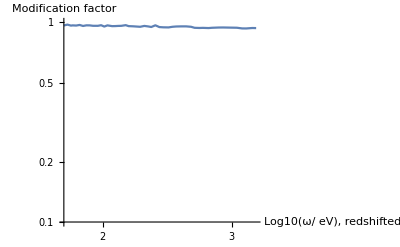

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];

(*Массив значений энергий*)
omegaVal={};

(*Интервал энергий*)
lowerBoundLow =-1;
upperBoundLow =1.5;

lowerBoundHigh=1.55;
upperBoundHigh=4;
step =0.05;

intervalKulkarniRedshifted={1.77,1.79,1.81,1.82,1.84,1.86,1.88,1.90,1.92,1.94,1.97,1.99,2.01,2.03,2.06,2.08,2.1,2.12,2.15,2.17,2.2,2.22,2.25,2.28,2.31,2.33,2.36,2.39,2.42,2.46,2.49,2.52,2.56,2.6,2.64,2.67,2.71,2.74,2.79,2.82,2.88,2.92,2.96,3.,3.05,3.1,3.14,3.2,3.24};

intervalKulkarniUnredshifted=intervalKulkarniRedshifted/Sqrt[(1-(4.134/R0))];


(*С каких углов считаем излучение*)
lowerAngle=0.1;
upperAngle=Pi/2.01;
nSteps=6;

(*Параметры АЛП*)
gMult=6;
gPower=-20;
mMult=4;
mPower=-6;
g=gMult*10^(gPower);
m=mMult*10^(mPower);

(*Конфигурация поля*)
angleObserver = Pi/3;
BSurf = 15*10^12;
R0 = 12;
period =7;

(*Конфигурация точки излучения*)
(*По x мы итерируемся, r - расстояние от поверхности звезды*)
r:=Sqrt[(R0 Sin[angleEmission]+x)^2 + (R0 Cos[angleEmission]+x Cot[alpha+angleEmission])^2];
angleIteration:=ArcTan[(R0 Sin[angleEmission]+x)/(R0 Cos[angleEmission]+x Cot[alpha+angleEmission])];

startingInclination:=Solve[1-Cos[alphaStartingInclination]==(1-Cos[angleObserver - angleEmission])(1-4.134/R0),alphaStartingInclination];

(*Радиус светового цилиндра*)
Rlc=47713*period;
upperLimit:=Rlc;

(*Значения поля (диполь)*)
(*Множитель плотности GJ*)
bRep:={bRad->BSurf*Cos[angleIteration]*(R0/r)^3,
	bTheta->0.5*BSurf*Sin[angleIteration]*(R0/r)^3,
	bPhi->0,
	GJfactor->1};


(*Элементы матрицы М*)
deltaMTheta:=5.0*10^7*bTheta*g;
deltaMPhi:=5.0*10^7*bPhi*g;
deltaMass:=2.5*10^9*m^2*(1/ω);
deltaPlasma:=GJfactor*3.1*10^(-12)*(bRad*Cos[angleIteration]-bTheta*Sin[angleIteration])*(1/period)*(1/ω);
deltaCEDTheta:=-4.5*10^(-22)*ω*bTheta^2;
deltaCEDPhi:=-4.5*10^(-22)*ω*bPhi^2;

(*Матрица М*)
mat:={{deltaPlasma+deltaCEDTheta,0,deltaMTheta},
	{0,deltaPlasma+deltaCEDPhi,deltaMPhi},
	{deltaMTheta,deltaMPhi,deltaMass}}/.bRep;

(*Матрица плотности ρ*)
rmat[x_]:={{r11[x],r12[x],r13[x]},{r21[x],r22[x],r23[x]},{r31[x],r32[x],r33[x]}};

(*Список начальных условий*)rmat0={{r11[0]==1,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==0,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};


tSpectrumLow= Table[
(*Энергия на поверхности*)
(*ω0:=10^(k);*)
ω0:=k;

(*С красным смещением*)
ω:=ω0*Sqrt[(1-(4.134/R0))/(1-(4.134/r))];

tSingle = Table[
(*Угол от 0 до 2.01*)
angleEmission=an;

unsignedAngles=alphaStartingInclination/.startingInclination[[2]];
sumAngles=unsignedAngles+angleEmission;

signs=Sign[angleObserver-unsignedAngles-angleEmission];
alpha=unsignedAngles*signs;

(*Решаем систему*)
eqs=NDSolve[Join[{ⅈ rmat'[x]==rmat[x].mat-mat.rmat[x]},rmat0],{r11[x],r22[x],r33[x]},{x,0,upperLimit}, MaxSteps->10^8, AccuracyGoal->5];

Re[r11[x]+r22[x]/.First[eqs]/.x->(upperLimit-1)]

,{an,lowerAngle,upperAngle,upperAngle/nSteps}];

Mean[tSingle]
,{k,intervalKulkarniUnredshifted}];

(*
tSpectrumHigh= Table[
(*Энергия на поверхности*)
ω0:=10^(k);

(*С красным смещением*)
ω:=ω0*Sqrt[(1-(4.134/R0))/(1-(4.134/r))];

(*Анизотропное излучение*)
angleEmission=angleObserver+0.01;

unsignedAngles=alphaStartingInclination/.startingInclination[[2]];
sumAngles=unsignedAngles+angleEmission;

signs=Sign[angleObserver-unsignedAngles-angleEmission];
alpha=unsignedAngles*signs;

(*Решаем систему*)
eqs=NDSolve[Join[{ⅈ rmat'[x]==rmat[x].mat-mat.rmat[x]},rmat0],{r11[x],r22[x],r33[x]},{x,0,upperLimit}, MaxSteps->10^8, AccuracyGoal->5];

Re[r11[x]+r22[x]/.First[eqs]/.x->(upperLimit-1)]
,{k,lowerBoundHigh,upperBoundHigh,step}];*)


Print["Time elapsed: ",AbsoluteTime[]-time];

(*totalRange=Join[Range[lowerBoundLow,upperBoundLow,step],Range[lowerBoundHigh,upperBoundHigh,step]];
totalSpectrum=Join[tSpectrumLow,tSpectrumHigh];*)

totalSpectrum=tSpectrumLow;

(*Строим ω с красным смещением*)
(*OmegaSurface:=10^x/.x->totalRange;
zFactor:=Sqrt[(1-(4.134/R0))];
OmegaInfinity:=OmegaSurface*zFactor;*)

OmegaInfinity:=intervalKulkarniRedshifted;

(*Строим график*)
data=Transpose[{OmegaInfinity,totalSpectrum}];
plot = ListLogLogPlot[data,PlotRange->{{Min[OmegaInfinity],Max[OmegaInfinity]},{0.1,1.0}},AxesLabel->{"Log10(ω/
eV),\nredshifted","Modification\nfactor"}, PlotMarkers->None,Joined->True]

(*Обычная шкала*)
(*dataToFile = Transpose[{10^x/.x->Range[lowerBound,upperBound,step],t}];*)

(*Логарифмическая шкала*)
dataToFile = Transpose[{OmegaInfinity,totalSpectrum}];

Export["Mixing_m_t"<>ToString[mMult]<>"_p"<>ToString[mPower]<>"__g_t"<>ToString[gMult]<>"_p"<>ToString[gPower]<>".dat",dataToFile,"Table"];
```

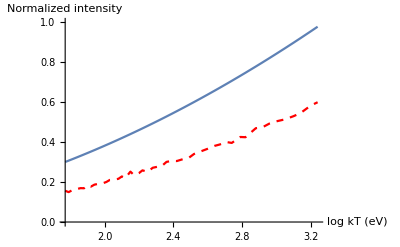

```mathematica
Clear["Global`*"]

(*Температура*)
T:=46;

(*Спектр ЧТ*)
Planck[w_]:=w^3/(4 Pi^3)/(Exp[w/T]-1);

(*Импорт данных*)
mixingResult = Import["Mixing.dat"];
energyValues=mixingResult[[All,1]];
mixingValues = mixingResult[[All,2]];

(*Расчет спектра ЧТ и нормализация*)
planckValues := Planck[energyValues]/Max[ Planck[energyValues]];

(*Расчет спектра со смешиванием*)
mixedPlanckValues=planckValues *mixingValues;

(*Коэффициенты кривой поглощения*)
c0[x_]:=Piecewise[{
{17.3,0.030<x<=0.100},
	{34.6,0.100<=x<0.284},
	{78.1,0.284<=x<0.400},
{71.4,0.400<=x<0.532},
	{95.5,0.532<=x<0.707},
	{308.9,0.707<=x<0.867},
	{120.6,0.867<=x<1.303},
	{141.3,1.303<=x<1.840},
	{202.7,1.840<=x<2.471},
	{342.7,2.471<=x<3.210},
	{352.2,3.210<=x<4.038},
	{433.9,4.038<=x<7.111},
	{629.0,7.111<=x<8.331},
	{701.2,8.331<=x<10.000}},0];
c1[x_]:=Piecewise[{
{608.1,0.030<x<=0.100},
	{267.9,0.100<=x<0.284},
	{18.8,0.284<=x<0.400},
{66.8,0.400<=x<0.532},
	{145.8,0.532<=x<0.707},
	{-380.6,0.707<=x<0.867},
	{169.3,0.867<=x<1.303},
	{146.8,1.303<=x<1.840},
	{104.7,1.840<=x<2.471},
	{18.7,2.471<=x<3.210},
	{18.7,3.210<=x<4.038},
	{-2.4,4.038<=x<7.111},
	{30.9,7.111<=x<8.331},
	{25.2,8.331<=x<10.000}},0];
c2[x_]:=Piecewise[{
{-2150.,0.030<x<=0.100},
	{-476.1,0.100<=x<0.284},
	{4.3,0.284<=x<0.400},
{-51.4,0.400<=x<0.532},
	{-61.1,0.532<=x<0.707},
	{294.0,0.707<=x<0.867},
	{-47.7,0.867<=x<1.303},
	{-31.5,1.303<=x<1.840},
	{-17.0,1.840<=x<2.471},
	{0.0,2.471<=x<3.210},
	{0.0,3.210<=x<4.038},
	{0.75,4.038<=x<7.111},
	{0.0,7.111<=x<8.331},
	{0.0,8.331<=x<10.000}},0];

(*Сигма, кол-во атомов водорода *)
sigma[energy_]:=(c0 [energy]energy+c1[energy] energy+c2[energy] energy^2)energy^(-3)*10^(-24);
Nh:=12.9*10^(19);

(*Кривая поглощения, переводим энергию в keV*)
extinctionCurve[energyEv_]:=Exp[-sigma[energyEv*0.001]*Nh];

(*Modification factor для поглощения*)
adsorbtionValues:=extinctionCurve/@energyValues;

(*Расчет спектра с поглощением*)
adsorbedPlanckValues=planckValues*adsorbtionValues;

(*Расчет смешанного спектра с поглощением*)
adsorbedMixedPlanckValues = mixedPlanckValues*adsorbtionValues;

(*Поглощение на пыли*)
(*Коэффициенты кривой поглощения*)

Fa[x_]:=Piecewise[ {{-0.04473(x-5.9)^2-0.009779(x-5.9)^3, 5.9≤x≤8}},
0];
Fb[x_]:=Piecewise[ {{0.2130(x-5.9)^2+0.1207(x-5.9)^3, 5.9≤x≤8}},
0];

a[x_]:=Piecewise[{
{0.574 x^(1.61),0.3<=x<1.1},
	{1+0.104*(x-1.82)-0.609*(x-1.82)^2+0.701*(x-1.82)^3+1.137*(x-1.82)^4-1.718*(x-1.82)^5-0.827*(x-1.82)^6+1.647*(x-1.82)^7-0.505*(x-1.82)^8,1.1<=x<3.3},
{1.752-0.316x-0.104/((x-4.67)^2+0.341)+Fa[x],3.3<=x<8},
{-1.073-0.628(x-8)+0.137(x-8)^2-0.070(x-8)^3,8≤x<=10}},
	0];
b[x_]:=Piecewise[{
{-0.527  x^(1.61),0.3<=x<1.1},
	{1.952*(x-1.82)+2.908*(x-1.82)^2-3.989*(x-1.82)^3-7.985*(x-1.82)^4+11.102*(x-1.82)^5+5.491*(x-1.82)^6-10.805*(x-1.82)^7+3.347*(x-1.82)^8,1.1<=x<3.3},
{-3.090+1.825x+1.206/((x-4.62)^2+0.263)+Fb[x],3.3<=x<8},
{13.670+4.257(x-8)-0.420(x-8)^2+0.374(x-8)^3,8≤x<=10}},
0];

Rv:=3.1;
extinctionCurveDustMkMeters[mkM_]:=10^(-0.4*0.12*(a[mkM]+b[mkM]/Rv));
extinctionCurveDustEv[eV_]:=extinctionCurveDustMkMeters[eV*0.197];

(*Modification factor для поглощения на пыли*)
adsorbtionValuesDust:=extinctionCurveDustEv/@energyValues;

(*Расчет спектра с поглощением*)
adsorbedPlanckValuesDust=adsorbedPlanckValues*adsorbtionValuesDust;
adsorbedMixedPlanckValuesDust:=adsorbedMixedPlanckValues*adsorbtionValuesDust;


(*Нижняя граница графика*)
minVal:=10^(-4);

(*Вывод графиков, energyValues для обычной, energyLogValues для логарифмической*)
plotUnmixed = ListLogLogPlot[Transpose[{energyValues, planckValues}],
PlotRange->{{Min[energyValues],Max[energyValues]},{minVal,1}},Joined->True];

plotMixed =  ListLogLogPlot[Transpose[{energyValues, mixedPlanckValues}],PlotStyle->{Red,Dashed},
PlotRange->{{Min[energyValues],Max[energyValues]},{minVal,1}},Joined->True];

plotUnmixedAdsorbed = ListPlot[Transpose[{energyValues, adsorbedPlanckValuesDust}],
PlotRange->{{Min[energyValues],Max[energyValues]},{minVal,1}},Joined->True];

plotMixedAdsorbed = ListPlot[Transpose[{energyValues, adsorbedMixedPlanckValuesDust}],PlotStyle->{Red,Dashed},
PlotRange->{{Min[energyValues],Max[energyValues]},{minVal,1}},Joined->True];


Show[plotUnmixedAdsorbed ,plotMixedAdsorbed , AxesLabel->{"log kT (eV)","Normalized intensity"} ]
```

```mathematica
10^(1.9)
```

79.4328

```mathematica
37.4/Sqrt[(1-(4.134/12))]
```

46.194

```mathematica
1/Sqrt[(1-(4.134/12))]
```

1.23513